## Bounds on Scalar-Tensor Theory From GW1510914

```mathematica
data1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"] (*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184},16330,{-0.960167,432.955,1.12358,4,0.423524,0.156429,0.304489}}
 |  |  |  |

```mathematica
data2=Import[NotebookDirectory[]<>"/-1pn-beta.csv","CSV"]  (*PPE beta*)
data3=Import[NotebookDirectory[]<>"/-1pn-alpha.csv","CSV"] (*PPE alpha*)
```

{{0.0000950433},{0.0000987158},{0.0000994462},{0.0000975037},{0.000095235},{0.000107632},{0.0000997691},16318,{0.0000986108},{0.0000999129},{0.0000988982},{0.0000984216},{0.000105075},{0.000104439},{0.000101563}}
 |  |  |  |

{{0.01842},{0.0193342},{0.0178007},{0.0192073},{0.0183703},{0.0168826},{0.0198715},{0.0176301},16317,{0.0177703},{0.0182836},{0.0180834},{0.0181399},{0.0177094},{0.0174525},{0.0190105}}
 |  |  |  |

```mathematica
Length[data3]
```

16332

```mathematica
χ1=data1[[All,7]]; (*Dimensionles spin parameter*)
χ2=data1[[All,8]];
```

```mathematica
DL=data1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,16318,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,16317,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
m1=data1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 ;
(*Ligo posterior gives mass in detector frame. We have to convert it source frame*)
```

```mathematica
m2=data1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.000154056,0.000150252,0.00013417,0.000166077,0.000153064,0.000129181,0.000164308,16318,0.000135998,0.000145104,0.000141122,0.000145081,0.000126583,0.000133266,0.000149862}
 |  |  |  |

```mathematica
η=(m1*m2)/(m1+m2)^2;
```

```mathematica
βppE=data2[[All,1]]/1.64485(*1-sigma upper bound*)
αppE=data3[[All,1]]/1.64485(*1-sigma upper bound*)
```

{0.0000577823,0.0000600151,0.0000604591,0.0000592781,0.0000578989,0.0000654359,0.0000606554,16319,0.0000607428,0.000060126,0.0000598362,0.0000638809,0.0000634943,0.0000617462}
 |  |  |  |

{0.0111986,0.0117544,0.0108221,0.0116773,0.0111684,0.0102639,0.012081,16318,0.0108036,0.0111157,0.010994,0.0110283,0.0107666,0.0106104,0.0115576}
 |  |  |  |

```mathematica
s1=(1+√(1-χ1^2))/2
s2=(1+√(1-χ2^2))/2
```

{0.959525,0.853652,0.999912,0.996693,0.957429,0.994472,0.998851,0.990716,16316,0.987879,0.908264,0.999229,0.999989,0.99078,0.686606,0.999659,0.996928}
 |  |  |  |

{0.999726,0.950278,0.977818,0.995736,0.971108,0.999458,0.958939,0.958736,16316,0.59088,0.981882,0.999959,0.999904,0.999962,0.914585,0.975786,0.952943}
 |  |  |  |

```mathematica
ϕdotSquared=Abs[-1792/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*βppE]
```

{2.61344×10^9,1.92328×10^9,1.24314×10^7,5.43027×10^10,1.74599×10^9,5.92236×10^6,1.06338×10^8,16318,3.8097×10^7,2.35019×10^7,2.74494×10^7,3.31217×10^7,7.51792×10^7,7.77249×10^6,2.13603×10^7}
 |  |  |  |

```mathematica
√Mean[ϕdotSquared]//ScientificForm (*one order of magnitude smaller than the bound of 1603.08955*)
```

6.81919×10^5

```mathematica
ϕdotSquaredamp=Abs[-48/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*αppE]
```

{1.3567×10^10,1.00899×10^10,5.96037×10^7,2.8653×10^11,9.02123×10^9,2.48825×10^7,5.67318×10^8,16318,1.83893×10^8,1.15199×10^8,1.3444×10^8,1.63516×10^8,3.39396×10^8,3.47903×10^7,1.07094×10^8}
 |  |  |  |

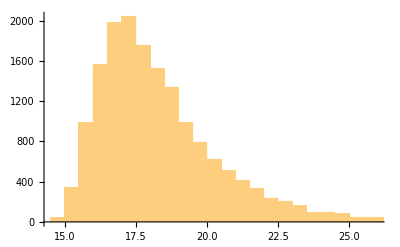

```mathematica
Histogram[Log[ϕdotSquared]]
```

ϕ̇ from phase correction:

```mathematica
LogSquaredϕdotPhase=Log[ϕdotSquared] (*This is Log of sigma_(alpha^2)*)
```

{22.1816,21.8749,16.8334,25.2155,21.7782,16.0919,18.9798,17.3769,16316,15.4068,17.9533,17.4702,17.6255,17.8133,18.633,16.3638,17.3747}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotPhase]
```

15.052

```mathematica
Max[LogSquaredϕdotPhase]
```

36.0147

```mathematica
𝒟logϕHist=HistogramDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕHist2=PDF[𝒟logϕHist,x];
```

```mathematica
𝒟logϕHist3[x_]=𝒟logϕHist2;
```

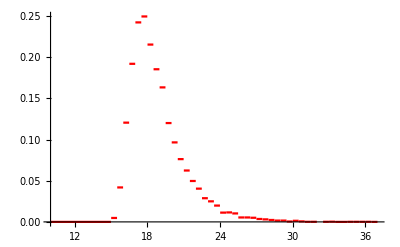

```mathematica
Plot1=Plot[𝒟logϕHist3[x],{x,10,37},PlotStyle->Red]
```

```mathematica
𝒟logϕdotSq=SmoothKernelDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSq2=PDF[𝒟logϕdotSq,x]
```

Piecewise[{{InterpolatingFunction[…][x], 13.8304≤x≤37.2363}, {0, True}}]

```mathematica
𝒟logϕdotSq3[x_]=𝒟logϕdotSq2
```

Piecewise[{{InterpolatingFunction[…][x], 13.8304≤x≤37.2363}, {0, True}}]

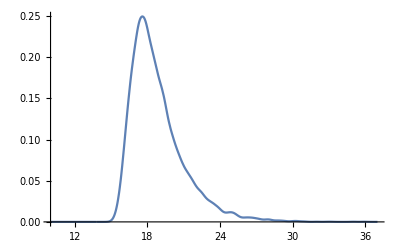

```mathematica
Plot2=Plot[𝒟logϕdotSq3[x],{x,10,37}]
```

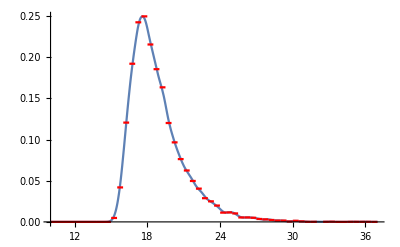

```mathematica
Show[Plot2,Plot1] (*SmoothKernelDistribution is good enough. We do not need to interpolate the acutual histogram*)
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
ϕdotSqLogSample=Prepend[10^Range[-1,11,0.1],0]
```

{0,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6,25118.9,31622.8,39810.7,50118.7,63095.7,79432.8,100000.,125893.,158489.,199526.,251189.,316228.,398107.,501187.,630957.,794328.,1.×10^6,1.25893×10^6,1.58489×10^6,1.99526×10^6,2.51189×10^6,3.16228×10^6,3.98107×10^6,5.01187×10^6,6.30957×10^6,7.94328×10^6,1.×10^7,1.25893×10^7,1.58489×10^7,1.99526×10^7,2.51189×10^7,3.16228×10^7,3.98107×10^7,5.01187×10^7,6.30957×10^7,7.94328×10^7,1.×10^8,1.25893×10^8,1.58489×10^8,1.99526×10^8,2.51189×10^8,3.16228×10^8,3.98107×10^8,5.01187×10^8,6.30957×10^8,7.94328×10^8,1.×10^9,1.25893×10^9,1.58489×10^9,1.99526×10^9,2.51189×10^9,3.16228×10^9,3.98107×10^9,5.01187×10^9,6.30957×10^9,7.94328×10^9,1.×10^10,1.25893×10^10,1.58489×10^10,1.99526×10^10,2.51189×10^10,3.16228×10^10,3.98107×10^10,5.01187×10^10,6.30957×10^10,7.94328×10^10,1.×10^11}

```mathematica
fun1ϕdotphaseTable[y_]=Table[{ϕdotSqLogSample[[i]],fun1αphase[ϕdotSqLogSample[[i]],y]},{i,1,Length[ϕdotSqLogSample]}];
```

```mathematica
ϕdotSqLogFinalPDFPhase=Table[{fun1ϕdotphaseTable[y][[i,1]],NIntegrate[fun1ϕdotphaseTable[y][[i,2]]*𝒟logϕdotSq3[y],{y,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]},{i,1,Length[fun1ϕdotphaseTable[y]]}]
```

{{0,9.32642×10^-9},{0.1,9.32642×10^-9},{0.125893,9.32642×10^-9},{0.158489,9.32642×10^-9},{0.199526,9.32642×10^-9},{0.251189,9.32642×10^-9},{0.316228,9.32642×10^-9},{0.398107,9.32642×10^-9},{0.501187,9.32642×10^-9},{0.630957,9.32642×10^-9},{0.794328,9.32642×10^-9},{1.,9.32642×10^-9},{1.25893,9.32642×10^-9},{1.58489,9.32642×10^-9},{1.99526,9.32642×10^-9},{2.51189,9.32642×10^-9},{3.16228,9.32642×10^-9},{3.98107,9.32642×10^-9},{5.01187,9.32642×10^-9},{6.30957,9.32642×10^-9},{7.94328,9.32642×10^-9},{10.,9.32642×10^-9},{12.5893,9.32642×10^-9},{15.8489,9.32642×10^-9},{19.9526,9.32642×10^-9},{25.1189,9.32642×10^-9},{31.6228,9.32642×10^-9},{39.8107,9.32642×10^-9},{50.1187,9.32642×10^-9},{63.0957,9.32642×10^-9},{79.4328,9.32642×10^-9},{100.,9.32642×10^-9},{125.893,9.32642×10^-9},{158.489,9.32642×10^-9},{199.526,9.32642×10^-9},{251.189,9.32642×10^-9},{316.228,9.32642×10^-9},{398.107,9.32642×10^-9},{501.187,9.32642×10^-9},{630.957,9.32642×10^-9},{794.328,9.32642×10^-9},{1000.,9.32642×10^-9},{1258.93,9.32642×10^-9},{1584.89,9.32642×10^-9},{1995.26,9.32642×10^-9},{2511.89,9.32642×10^-9},{3162.28,9.32642×10^-9},{3981.07,9.32642×10^-9},{5011.87,9.32642×10^-9},{6309.57,9.32642×10^-9},{7943.28,9.32642×10^-9},{10000.,9.32642×10^-9},{12589.3,9.32642×10^-9},{15848.9,9.32641×10^-9},{19952.6,9.32641×10^-9},{25118.9,9.3264×10^-9},{31622.8,9.32639×10^-9},{39810.7,9.32637×10^-9},{50118.7,9.32633×10^-9},{63095.7,9.32628×10^-9},{79432.8,9.32619×10^-9},{100000.,9.32605×10^-9},{125893.,9.32584×10^-9},{158489.,9.32549×10^-9},{199526.,9.32495×10^-9},{251189.,9.32408×10^-9},{316228.,9.32271×10^-9},{398107.,9.32054×10^-9},{501187.,9.31711×10^-9},{630957.,9.31168×10^-9},{794328.,9.30309×10^-9},{1.×10^6,9.28956×10^-9},{1.25893×10^6,9.26826×10^-9},{1.58489×10^6,9.2349×10^-9},{1.99526×10^6,9.18298×10^-9},{2.51189×10^6,9.10296×10^-9},{3.16228×10^6,8.98144×10^-9},{3.98107×10^6,8.80074×10^-9},{5.01187×10^6,8.53976×10^-9},{6.30957×10^6,8.17704×10^-9},{7.94328×10^6,7.6965×10^-9},{1.×10^7,7.09452×10^-9},{1.25893×10^7,6.38541×10^-9},{1.58489×10^7,5.60163×10^-9},{1.99526×10^7,4.78753×10^-9},{2.51189×10^7,3.98937×10^-9},{3.16228×10^7,3.24584×10^-9},{3.98107×10^7,2.58287×10^-9},{5.01187×10^7,2.01348×10^-9},{6.30957×10^7,1.54052×10^-9},{7.94328×10^7,1.15973×10^-9},{1.×10^8,8.61833×10^-10},{1.25893×10^8,6.34344×10^-10},{1.58489×10^8,4.63654×10^-10},{1.99526×10^8,3.36984×10^-10},{2.51189×10^8,2.43614×10^-10},{3.16228×10^8,1.75186×10^-10},{3.98107×10^8,1.25373×10^-10},{5.01187×10^8,8.94105×10^-11},{6.30957×10^8,6.36819×10^-11},{7.94328×10^8,4.54011×10^-11},{1.×10^9,3.24316×10^-11},{1.25893×10^9,2.32047×10^-11},{1.58489×10^9,1.66182×10^-11},{1.99526×10^9,1.19047×10^-11},{2.51189×10^9,8.52399×10^-12},{3.16228×10^9,6.09447×10^-12},{3.98107×10^9,4.34726×10^-12},{5.01187×10^9,3.09313×10^-12},{6.30957×10^9,2.1964×10^-12},{7.94328×10^9,1.55733×10^-12},{1.×10^10,1.10257×10^-12},{1.25893×10^10,7.79385×10^-13},{1.58489×10^10,5.50227×10^-13},{1.99526×10^10,3.87979×10^-13},{2.51189×10^10,2.7317×10^-13},{3.16228×10^10,1.9224×10^-13},{3.98107×10^10,1.35689×10^-13},{5.01187×10^10,9.64717×10^-14},{6.30957×10^10,6.91684×10^-14},{7.94328×10^10,4.97724×10^-14},{1.×10^11,3.5636×10^-14}}

```mathematica
ϕdotSqLogFinalPDFPhaseInterp=Interpolation[ϕdotSqLogFinalPDFPhase]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalization=NIntegrate[ϕdotSqLogFinalPDFPhaseInterp[x],{x,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]
```

0.49218

```mathematica
ϕdotSqLogFinalPDFPhaseNorm=Table[{ϕdotSqLogFinalPDFPhase[[i,1]],ϕdotSqLogFinalPDFPhase[[i,2]]/ϕdotSqNormalization},{i,1,Length[ϕdotSqLogFinalPDFPhase]}];
```

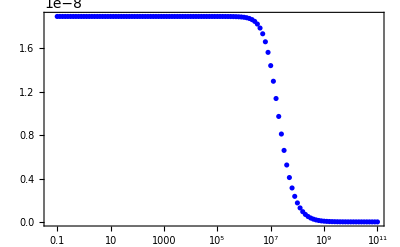

```mathematica
plotϕdotSqFinalPDFPhaseLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFPhaseNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFPhaseInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFPhaseNorm=Table[{ϕdotSqLogSample[[i]],NIntegrate[ϕdotSqFinalPDFPhaseInterpLogNorm[x],{x,Min[ϕdotSqLogSample],ϕdotSqLogSample[[i]]}]},{i,1,Length[ϕdotSqLogSample]}];
```

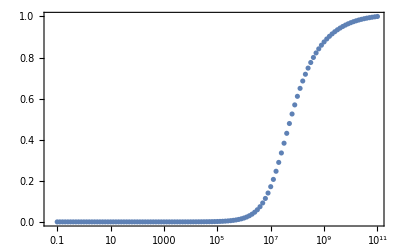

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFPhaseNormInterp=Interpolation[ϕdotSqFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLphase=x/.FindRoot[ϕdotSqFinalCDFPhaseNormInterp[x]==0.9,{x,10^8}]
```

1.48823×10^9

```mathematica
√ϕdotSq90CLphase//ScientificForm
```

3.85776×10^4

```mathematica
ϕ̇ from amplitude correction:
```

```mathematica
LogSquaredϕdotamp=Log[ϕdotSquaredamp]
```

{23.3309,23.0348,17.9032,26.3811,22.9228,17.0297,20.1564,18.4565,16316,16.4814,19.0299,18.5622,18.7166,18.9124,19.6427,17.3649,18.4892}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotamp]
```

15.9326

```mathematica
Max[LogSquaredϕdotamp]
```

37.1655

```mathematica
Histogram[LogSquaredϕdotamp];
```

```mathematica
𝒟logϕdotSqamp=SmoothKernelDistribution[LogSquaredϕdotamp]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSqamp2=PDF[𝒟logϕdotSqamp,x]
```

Piecewise[{{InterpolatingFunction[…][x], 14.6859≤x≤38.4122}, {0, True}}]

```mathematica
𝒟logϕdotSqamp3[x_]=𝒟logϕdotSqamp2
```

Piecewise[{{InterpolatingFunction[…][x], 14.6859≤x≤38.4122}, {0, True}}]

```mathematica
Plot2=Plot[𝒟logϕdotSqamp3[x],{x,7,40},PlotRange->All];
```

```mathematica
ϕdotSqLogSampleamp=Prepend[10^Range[-1,11,0.1],0];
```

```mathematica
fun1ϕdotampTable[y_]=Table[{ϕdotSqLogSampleamp[[i]],fun1αphase[ϕdotSqLogSampleamp[[i]],y]},{i,1,Length[ϕdotSqLogSampleamp]}];
```

```mathematica
ϕdotSqLogFinalPDFamp=Table[{fun1ϕdotampTable[y][[i,1]],NIntegrate[fun1ϕdotampTable[y][[i,2]]*𝒟logϕdotSqamp3[y],{y,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]},{i,1,Length[fun1ϕdotampTable[y]]}]
```

{{0,3.20183×10^-9},{0.1,3.20183×10^-9},{0.125893,3.20183×10^-9},{0.158489,3.20183×10^-9},{0.199526,3.20183×10^-9},{0.251189,3.20183×10^-9},{0.316228,3.20183×10^-9},{0.398107,3.20183×10^-9},{0.501187,3.20183×10^-9},{0.630957,3.20183×10^-9},{0.794328,3.20183×10^-9},{1.,3.20183×10^-9},{1.25893,3.20183×10^-9},{1.58489,3.20183×10^-9},{1.99526,3.20183×10^-9},{2.51189,3.20183×10^-9},{3.16228,3.20183×10^-9},{3.98107,3.20183×10^-9},{5.01187,3.20183×10^-9},{6.30957,3.20183×10^-9},{7.94328,3.20183×10^-9},{10.,3.20183×10^-9},{12.5893,3.20183×10^-9},{15.8489,3.20183×10^-9},{19.9526,3.20183×10^-9},{25.1189,3.20183×10^-9},{31.6228,3.20183×10^-9},{39.8107,3.20183×10^-9},{50.1187,3.20183×10^-9},{63.0957,3.20183×10^-9},{79.4328,3.20183×10^-9},{100.,3.20183×10^-9},{125.893,3.20183×10^-9},{158.489,3.20183×10^-9},{199.526,3.20183×10^-9},{251.189,3.20183×10^-9},{316.228,3.20183×10^-9},{398.107,3.20183×10^-9},{501.187,3.20183×10^-9},{630.957,3.20183×10^-9},{794.328,3.20183×10^-9},{1000.,3.20183×10^-9},{1258.93,3.20183×10^-9},{1584.89,3.20183×10^-9},{1995.26,3.20183×10^-9},{2511.89,3.20183×10^-9},{3162.28,3.20183×10^-9},{3981.07,3.20183×10^-9},{5011.87,3.20183×10^-9},{6309.57,3.20183×10^-9},{7943.28,3.20183×10^-9},{10000.,3.20183×10^-9},{12589.3,3.20183×10^-9},{15848.9,3.20183×10^-9},{19952.6,3.20183×10^-9},{25118.9,3.20183×10^-9},{31622.8,3.20183×10^-9},{39810.7,3.20183×10^-9},{50118.7,3.20183×10^-9},{63095.7,3.20182×10^-9},{79432.8,3.20182×10^-9},{100000.,3.20181×10^-9},{125893.,3.2018×10^-9},{158489.,3.20179×10^-9},{199526.,3.20176×10^-9},{251189.,3.20172×10^-9},{316228.,3.20165×10^-9},{398107.,3.20154×10^-9},{501187.,3.20138×10^-9},{630957.,3.20111×10^-9},{794328.,3.20069×10^-9},{1.×10^6,3.20002×10^-9},{1.25893×10^6,3.19897×10^-9},{1.58489×10^6,3.1973×10^-9},{1.99526×10^6,3.19466×10^-9},{2.51189×10^6,3.19049×10^-9},{3.16228×10^6,3.18394×10^-9},{3.98107×10^6,3.17368×10^-9},{5.01187×10^6,3.15771×10^-9},{6.30957×10^6,3.13309×10^-9},{7.94328×10^6,3.09568×10^-9},{1.×10^7,3.03999×10^-9},{1.25893×10^7,2.95936×10^-9},{1.58489×10^7,2.84683×10^-9},{1.99526×10^7,2.69671×10^-9},{2.51189×10^7,2.50676×10^-9},{3.16228×10^7,2.28011×10^-9},{3.98107×10^7,2.02573×10^-9},{5.01187×10^7,1.75694×10^-9},{6.30957×10^7,1.48837×10^-9},{7.94328×10^7,1.23288×10^-9},{1.×10^8,9.99741×10^-10},{1.25893×10^8,7.94437×10^-10},{1.58489×10^8,6.19342×10^-10},{1.99526×10^8,4.74503×10^-10},{2.51189×10^8,3.58165×10^-10},{3.16228×10^8,2.67183×10^-10},{3.98107×10^8,1.97547×10^-10},{5.01187×10^8,1.45039×10^-10},{6.30957×10^8,1.05818×10^-10},{7.94328×10^8,7.6717×10^-11},{1.×10^9,5.52771×10^-11},{1.25893×10^9,3.96125×10^-11},{1.58489×10^9,2.82755×10^-11},{1.99526×10^9,2.01515×10^-11},{2.51189×10^9,1.43734×10^-11},{3.16228×10^9,1.02719×10^-11},{3.98107×10^9,7.35288×10^-12},{5.01187×10^9,5.26797×10^-12},{6.30957×10^9,3.77478×10^-12},{7.94328×10^9,2.70314×10^-12},{1.×10^10,1.93266×10^-12},{1.25893×10^10,1.37842×10^-12},{1.58489×10^10,9.80542×10^-13},{1.99526×10^10,6.96109×10^-13},{2.51189×10^10,4.9351×10^-13},{3.16228×10^10,3.49422×10^-13},{3.98107×10^10,2.47045×10^-13},{5.01187×10^10,1.74444×10^-13},{6.30957×10^10,1.23037×10^-13},{7.94328×10^10,8.66638×10^-14},{1.×10^11,6.1024×10^-14}}

```mathematica
ϕdotSqLogFinalPDFampInterp=Interpolation[ϕdotSqLogFinalPDFamp]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalizationamp=NIntegrate[ϕdotSqLogFinalPDFampInterp[x],{x,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]
```

0.486766

```mathematica
ϕdotSqLogFinalPDFampNorm=Table[{ϕdotSqLogFinalPDFamp[[i,1]],ϕdotSqLogFinalPDFamp[[i,2]]/ϕdotSqNormalizationamp},{i,1,Length[ϕdotSqLogFinalPDFamp]}]
```

{{0,6.57776×10^-9},{0.1,6.57776×10^-9},{0.125893,6.57776×10^-9},{0.158489,6.57776×10^-9},{0.199526,6.57776×10^-9},{0.251189,6.57776×10^-9},{0.316228,6.57776×10^-9},{0.398107,6.57776×10^-9},{0.501187,6.57776×10^-9},{0.630957,6.57776×10^-9},{0.794328,6.57776×10^-9},{1.,6.57776×10^-9},{1.25893,6.57776×10^-9},{1.58489,6.57776×10^-9},{1.99526,6.57776×10^-9},{2.51189,6.57776×10^-9},{3.16228,6.57776×10^-9},{3.98107,6.57776×10^-9},{5.01187,6.57776×10^-9},{6.30957,6.57776×10^-9},{7.94328,6.57776×10^-9},{10.,6.57776×10^-9},{12.5893,6.57776×10^-9},{15.8489,6.57776×10^-9},{19.9526,6.57776×10^-9},{25.1189,6.57776×10^-9},{31.6228,6.57776×10^-9},{39.8107,6.57776×10^-9},{50.1187,6.57776×10^-9},{63.0957,6.57776×10^-9},{79.4328,6.57776×10^-9},{100.,6.57776×10^-9},{125.893,6.57776×10^-9},{158.489,6.57776×10^-9},{199.526,6.57776×10^-9},{251.189,6.57776×10^-9},{316.228,6.57776×10^-9},{398.107,6.57776×10^-9},{501.187,6.57776×10^-9},{630.957,6.57776×10^-9},{794.328,6.57776×10^-9},{1000.,6.57776×10^-9},{1258.93,6.57776×10^-9},{1584.89,6.57776×10^-9},{1995.26,6.57776×10^-9},{2511.89,6.57776×10^-9},{3162.28,6.57776×10^-9},{3981.07,6.57776×10^-9},{5011.87,6.57776×10^-9},{6309.57,6.57776×10^-9},{7943.28,6.57776×10^-9},{10000.,6.57776×10^-9},{12589.3,6.57776×10^-9},{15848.9,6.57776×10^-9},{19952.6,6.57776×10^-9},{25118.9,6.57776×10^-9},{31622.8,6.57776×10^-9},{39810.7,6.57776×10^-9},{50118.7,6.57775×10^-9},{63095.7,6.57775×10^-9},{79432.8,6.57774×10^-9},{100000.,6.57773×10^-9},{125893.,6.5777×10^-9},{158489.,6.57767×10^-9},{199526.,6.57761×10^-9},{251189.,6.57753×10^-9},{316228.,6.57739×10^-9},{398107.,6.57717×10^-9},{501187.,6.57683×10^-9},{630957.,6.57628×10^-9},{794328.,6.57542×10^-9},{1.×10^6,6.57405×10^-9},{1.25893×10^6,6.57188×10^-9},{1.58489×10^6,6.56844×10^-9},{1.99526×10^6,6.56302×10^-9},{2.51189×10^6,6.55447×10^-9},{3.16228×10^6,6.54101×10^-9},{3.98107×10^6,6.51993×10^-9},{5.01187×10^6,6.48712×10^-9},{6.30957×10^6,6.43654×10^-9},{7.94328×10^6,6.35969×10^-9},{1.×10^7,6.24528×10^-9},{1.25893×10^7,6.07964×10^-9},{1.58489×10^7,5.84846×10^-9},{1.99526×10^7,5.54005×10^-9},{2.51189×10^7,5.14982×10^-9},{3.16228×10^7,4.68419×10^-9},{3.98107×10^7,4.1616×10^-9},{5.01187×10^7,3.60941×10^-9},{6.30957×10^7,3.05766×10^-9},{7.94328×10^7,2.53279×10^-9},{1.×10^8,2.05384×10^-9},{1.25893×10^8,1.63207×10^-9},{1.58489×10^8,1.27236×10^-9},{1.99526×10^8,9.74807×10^-10},{2.51189×10^8,7.35805×10^-10},{3.16228×10^8,5.48895×10^-10},{3.98107×10^8,4.05835×10^-10},{5.01187×10^8,2.97965×10^-10},{6.30957×10^8,2.1739×10^-10},{7.94328×10^8,1.57606×10^-10},{1.×10^9,1.1356×10^-10},{1.25893×10^9,8.13789×10^-11},{1.58489×10^9,5.80884×10^-11},{1.99526×10^9,4.13988×10^-11},{2.51189×10^9,2.95283×10^-11},{3.16228×10^9,2.11023×10^-11},{3.98107×10^9,1.51056×10^-11},{5.01187×10^9,1.08224×10^-11},{6.30957×10^9,7.75481×10^-12},{7.94328×10^9,5.55326×10^-12},{1.×10^10,3.97041×10^-12},{1.25893×10^10,2.83179×10^-12},{1.58489×10^10,2.0144×10^-12},{1.99526×10^10,1.43007×10^-12},{2.51189×10^10,1.01386×10^-12},{3.16228×10^10,7.17844×10^-13},{3.98107×10^10,5.07523×10^-13},{5.01187×10^10,3.58373×10^-13},{6.30957×10^10,2.52764×10^-13},{7.94328×10^10,1.7804×10^-13},{1.×10^11,1.25366×10^-13}}

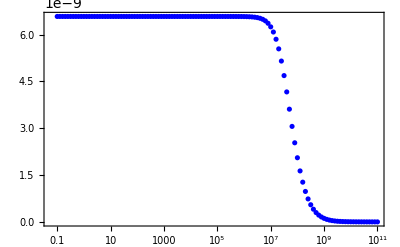

```mathematica
plotϕdotSqFinalPDFampLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFampNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFampInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFampNorm=Table[{ϕdotSqLogSampleamp[[i]],NIntegrate[ϕdotSqFinalPDFampInterpLogNorm[x],{x,Min[ϕdotSqLogSampleamp],ϕdotSqLogSampleamp[[i]]}]},{i,1,Length[ϕdotSqLogSampleamp]}]
```

{{0,0},{0.1,6.57776×10^-10},{0.125893,8.28091×10^-10},{0.158489,1.04251×10^-9},{0.199526,1.31244×10^-9},{0.251189,1.65226×10^-9},{0.316228,2.08007×10^-9},{0.398107,2.61865×10^-9},{0.501187,3.29669×10^-9},{0.630957,4.15029×10^-9},{0.794328,5.2249×10^-9},{1.,6.57776×10^-9},{1.25893,8.28091×10^-9},{1.58489,1.04251×10^-8},{1.99526,1.31244×10^-8},{2.51189,1.65226×10^-8},{3.16228,2.08007×10^-8},{3.98107,2.61865×10^-8},{5.01187,3.29669×10^-8},{6.30957,4.15029×10^-8},{7.94328,5.2249×10^-8},{10.,6.57776×10^-8},{12.5893,8.28091×10^-8},{15.8489,1.04251×10^-7},{19.9526,1.31244×10^-7},{25.1189,1.65226×10^-7},{31.6228,2.08007×10^-7},{39.8107,2.61865×10^-7},{50.1187,3.29669×10^-7},{63.0957,4.15029×10^-7},{79.4328,5.2249×10^-7},{100.,6.57776×10^-7},{125.893,8.28091×10^-7},{158.489,1.04251×10^-6},{199.526,1.31244×10^-6},{251.189,1.65226×10^-6},{316.228,2.08007×10^-6},{398.107,2.61865×10^-6},{501.187,3.29669×10^-6},{630.957,4.15029×10^-6},{794.328,5.2249×10^-6},{1000.,6.57776×10^-6},{1258.93,8.28091×10^-6},{1584.89,0.0000104251},{1995.26,0.0000131244},{2511.89,0.0000165226},{3162.28,0.0000208007},{3981.07,0.0000261865},{5011.87,0.0000329669},{6309.57,0.0000415029},{7943.28,0.000052249},{10000.,0.0000657776},{12589.3,0.0000828091},{15848.9,0.000104251},{19952.6,0.000131244},{25118.9,0.000165226},{31622.8,0.000208007},{39810.7,0.000261865},{50118.7,0.000329669},{63095.7,0.000415028},{79432.8,0.00052249},{100000.,0.000657775},{125893.,0.000828089},{158489.,0.0010425},{199526.,0.00131243},{251189.,0.00165224},{316228.,0.00208003},{398107.,0.00261858},{501187.,0.00329653},{630957.,0.00414998},{794328.,0.00522428},{1.×10^6,0.00657652},{1.25893×10^6,0.00827844},{1.58489×10^6,0.0104201},{1.99526×10^6,0.0131145},{2.51189×10^6,0.016503},{3.16228×10^6,0.0207618},{3.98107×10^6,0.0261092},{5.01187×10^6,0.0328136},{6.30957×10^6,0.0412002},{7.94328×10^6,0.0516547},{1.×10^7,0.0646202},{1.25893×10^7,0.0805808},{1.58489×10^7,0.100027},{1.99526×10^7,0.123399},{2.51189×10^7,0.151009},{3.16228×10^7,0.18297},{3.98107×10^7,0.219135},{5.01187×10^7,0.259091},{6.30957×10^7,0.302196},{7.94328×10^7,0.34764},{1.×10^8,0.394514},{1.25893×10^8,0.441872},{1.58489×10^8,0.488785},{1.99526×10^8,0.534414},{2.51189×10^8,0.57808},{3.16228×10^8,0.619313},{3.98107×10^8,0.657848},{5.01187×10^8,0.693582},{6.30957×10^8,0.726503},{7.94328×10^8,0.756644},{1.×10^9,0.784067},{1.25893×10^9,0.808871},{1.58489×10^9,0.831199},{1.99526×10^9,0.851242},{2.51189×10^9,0.869227},{3.16228×10^9,0.88539},{3.98107×10^9,0.899945},{5.01187×10^9,0.913069},{6.30957×10^9,0.924908},{7.94328×10^9,0.935585},{1.×10^10,0.945204},{1.25893×10^10,0.953853},{1.58489×10^10,0.961608},{1.99526×10^10,0.968545},{2.51189×10^10,0.97474},{3.16228×10^10,0.980266},{3.98107×10^10,0.985188},{5.01187×10^10,0.989566},{6.30957×10^10,0.993456},{7.94328×10^10,0.996907},{1.×10^11,1.}}

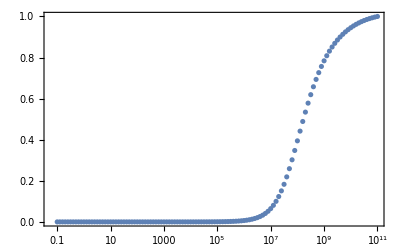

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFampNormInterp=Interpolation[ϕdotSqFinalCDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLamp=x/.FindRoot[ϕdotSqFinalCDFampNormInterp[x]==0.9,{x,10^9}]
```

3.98467×10^9

```mathematica
√ϕdotSq90CLamp//ScientificForm
```

6.31243×10^4